```mathematica
sofTϕM1 = Import["C:\\Users\\pedro\\Desktop\\ESTUDIOS\\PhD in Theoretical Physics\\1 year\\S(T) Neural Network\\Python Cacharreo run 2\\Curve_sofT_case3of5.csv"][[;; ;; 2]];
```

```mathematica
AppendTo[sofTϕM1,{0,0}];
```

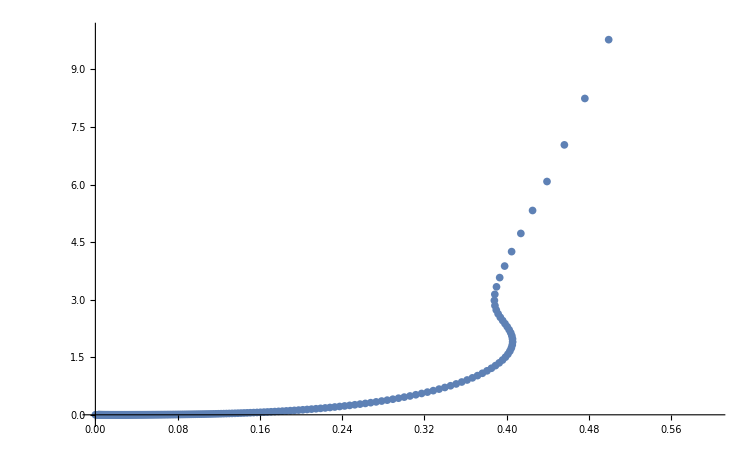

```mathematica
p1 = ListPlot[sofTϕM1,PlotRange->{{0,0.6},{-0.1,10}}]
```

```mathematica
Manipulate[Plot[0.3*(1/2+1/2 * Tanh[k*(-x+0.4)]),{x,-1,1}],{k,1,50}] (* Continous parametrization of a Θ *)
```

```mathematica
Manipulate[Plot[0.2*(Exp[-(x-2)/k]),{x,0,5},PlotRange->{{0,5},{0,2}}],{k,1,50}]
```

```mathematica
sofTϕM1Moved = {};
Do[AppendTo[sofTϕM1Moved,{sofTϕM1[[i,1]] + 0.4(1/2 +1/2 * Tanh[-5*(sofTϕM1[[i,1]] - 0.005)]),sofTϕM1[[i,2]]}],{i,Length[sofTϕM1]}]
```

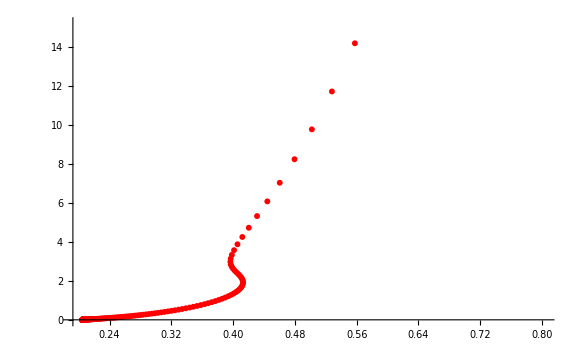

```mathematica
p2 =ListPlot[sofTϕM1Moved,PlotStyle->Red]
```

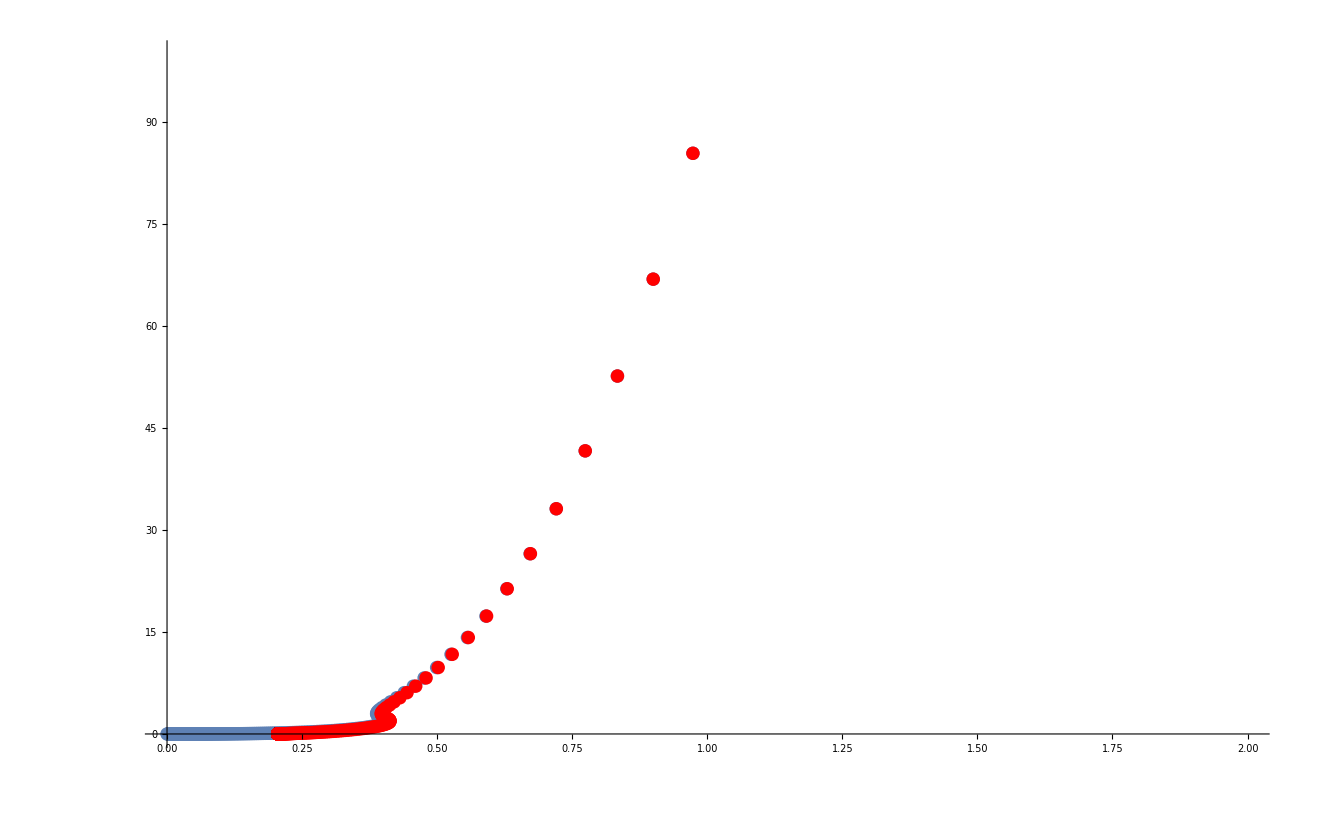

```mathematica
Show[p1,p2,PlotRange->{{0,2},{0,100}}]
```

```mathematica
sofTϕM1Moved
```

{{70.8465,3.46379×10^7},{64.1213,2.56804×10^7},{58.0361,1.90409×10^7},{52.5299,1.41193×10^7},{47.5478,1.04708×10^7},{43.0397,7.76599×10^6},{38.9607,5.76057×10^6},{35.2698,4.27359×10^6},{31.9302,3.17091×10^6},{28.9084,2.35313×10^6},{26.1741,1.74657×10^6},{23.7001,1.29662×10^6},{21.4615,962801.},{19.436,715096.},{17.6032,531261.},{15.9448,394803.},{14.4443,293490.},{13.0866,218253.},{11.8581,162368.},{10.7465,120845.},{9.74075,89984.},{8.83072,67039.4},{8.00731,49974.3},{7.26229,37276.9},{6.5882,27825.1},{5.97829,20785.9},{5.42646,15540.5},{4.92718,11629.7},{4.47546,8711.82},{4.06678,6533.32},{3.69704,4905.56},{3.36254,3688.26},{3.05994,2777.07},{2.78621,2094.31},{2.53859,1582.15},{2.31463,1197.49},{2.11206,908.211},{1.92887,690.346},{1.76321,526.009},{1.61343,401.84},{1.47802,307.848},{1.35563,236.56},{1.24503,182.376},{1.14512,141.101},{1.05489,109.582},{0.97344,85.4525},{0.899972,66.9301},{0.83376,52.6721},{0.774162,41.6651},{0.720609,33.1427},{0.672598,26.5248},{0.629688,21.3708},{0.591491,17.3457},{0.557664,14.1942},{0.527903,11.7208},{0.501932,9.77558},{0.479496,8.24311},{0.460352,7.03407},{0.444261,6.07907},{0.430988,5.32394},{0.420291,4.72618},{0.411925,4.25228},{0.405645,3.87572},{0.401201,3.57537},{0.398347,3.33438},{0.396842,3.13926},{0.396452,2.97917},{0.396954,2.84542},{0.398136,2.73107},{0.399803,2.6306},{0.401771,2.53967},{0.40388,2.45495},{0.405983,2.37393},{0.407955,2.29481},{0.409692,2.21635},{0.411107,2.13779},{0.412135,2.05875},{0.412728,1.97913},{0.412854,1.89904},{0.412499,1.81874},{0.411659,1.73858},{0.410343,1.65895},{0.408569,1.58024},{0.40636,1.50285},{0.403747,1.42712},{0.400762,1.35335},{0.397442,1.2818},{0.393822,1.21268},{0.389939,1.14614},{0.385829,1.08228},{0.381525,1.02117},{0.377062,0.962834},{0.37247,0.907277},{0.367778,0.854467},{0.363013,0.804354},{0.358198,0.756872},{0.353356,0.711941},{0.348507,0.669474},{0.343669,0.629373},{0.338858,0.591541},{0.334089,0.555875},{0.329374,0.522273},{0.324724,0.490633},{0.320149,0.460853},{0.315658,0.432837},{0.311257,0.406489},{0.306952,0.381717},{0.30275,0.358433},{0.298653,0.336552},{0.294665,0.315993},{0.290789,0.29668},{0.287026,0.278538},{0.283379,0.261501},{0.279847,0.2455},{0.27643,0.230475},{0.27313,0.216367},{0.269945,0.203121},{0.266874,0.190685},{0.263917,0.179009},{0.26107,0.168047},{0.258334,0.157756},{0.255705,0.148096},{0.253182,0.139027},{0.250763,0.130513},{0.248445,0.122521},{0.246225,0.115019},{0.244101,0.107976},{0.24207,0.101365},{0.240129,0.0951583},{0.238276,0.0893323},{0.236509,0.0838632},{0.234823,0.0787291},{0.233216,0.0739096},{0.231686,0.0693853},{0.230229,0.0651381},{0.228843,0.0611511},{0.227525,0.0574083},{0.226273,0.0538946},{0.225084,0.0505962},{0.223955,0.0474998},{0.222883,0.0445929},{0.221867,0.041864},{0.220904,0.0393022},{0.219991,0.0368973},{0.219127,0.0346396},{0.218308,0.03252},{0.217533,0.0305303},{0.216801,0.0286623},{0.216108,0.0269086},{0.215453,0.0252623},{0.214834,0.0237167},{0.214249,0.0222657},{0.213697,0.0209036},{0.213176,0.0196247},{0.212685,0.0184242},{0.212221,0.0172971},{0.211784,0.0162389},{0.211371,0.0152455},{0.210983,0.0143129},{0.210617,0.0134373},{0.210272,0.0126154},{0.209947,0.0118437},{0.209642,0.0111192},{0.209354,0.010439},{0.209083,0.00980046},{0.208829,0.00920098},{0.208589,0.00863816},{0.208364,0.00810978},{0.208153,0.00761372},{0.207954,0.00714801},{0.207767,0.00671079},{0.207591,0.00630031},{0.207426,0.00591494},{0.207272,0.00555314},{0.207126,0.00521348},{0.20699,0.00489459},{0.206862,0.00459521},{0.206742,0.00431414},{0.206629,0.00405026},{0.206523,0.00380253},{0.206424,0.00356995},{0.206331,0.00335159},{0.206244,0.00314659},{0.206163,0.00295413},{0.206086,0.00277344},{0.206015,0.00260381},{0.205948,0.00244454},{0.205885,0.00229503},{0.205826,0.00215465},{0.205771,0.00202286},{0.205719,0.00189914},{0.205671,0.00178298},{0.205626,0.00167392},{0.205584,0.00157154},{0.205544,0.00147542},{0.205507,0.00138518},{0.205473,0.00130045},{0.205441,0.00122091},{0.20541,0.00114624},{0.205382,0.00107613},{0.205356,0.00101031},{0.205331,0.000948516},{0.205308,0.000890501},{0.205287,0.000836035},{0.205267,0.0007849},{0.205248,0.000736893},{0.205231,0.000691822},{0.205214,0.000649508},{0.205199,0.000609782},{0.205185,0.000572485},{0.205172,0.00053747},{0.20516,0.000504597},{0.205148,0.000473734},{0.205137,0.000444759},{0.205127,0.000417556},{0.205118,0.000392017},{0.205109,0.000368039},{0.205101,0.000345529},{0.205094,0.000324395},{0.205087,0.000304554},{0.20508,0.000285927},{0.205074,0.000268438},{0.205069,0.00025202},{0.205064,0.000236605},{0.205059,0.000222134},{0.205054,0.000208547},{0.20505,0.000195792},{0.205046,0.000183817},{0.205043,0.000172574},{0.205039,0.000162019},{0.205036,0.000152109},{0.205033,0.000142806},{0.205031,0.000134071},{0.205028,0.000125871},{0.205026,0.000118172},{0.205024,0.000110944},{0.205022,0.000104159},{0.20502,0.000097788},{0.205018,0.000091807},{0.205017,0.0000861918},{0.205015,0.00008092},{0.205014,0.0000759707},{0.205013,0.000071324},{0.205012,0.0000669616},{0.205011,0.000062866},{0.20501,0.0000590209},{0.205009,0.000055411},{0.205008,0.0000520219},{0.205007,0.0000488401},{0.205007,0.0000458529},{0.205006,0.0000430484},{0.205006,0.0000404154},{0.205005,0.0000379434},{0.205005,0.0000356227},{0.205004,0.0000334439},{0.205004,0.0000313984},{0.205003,0.0000294779},{0.205003,0.000027675},{0.205003,0.0000259823},{0.205002,0.0000243931},{0.205002,0.0000229012},{0.205002,0.0000215004},{0.205002,0.0000201854},{0.205002,0.0000189508},{0.205001,0.0000177917},{0.205001,0.0000167035},{0.205001,0.0000156819},{0.205001,0.0000147227},{0.205001,0.0000138222},{0.205001,0.0000129768},{0.205001,0.0000121831},{0.205001,0.0000114379},{0.205,0.0000107384},{0.205,0.0000100816},{0.205,9.46495×10^-6},{0.205,8.88605×10^-6},{0.205,8.34255×10^-6},{0.205,7.83229×10^-6},{0.205,7.35324×10^-6},{0.205,6.90349×10^-6},{0.205,6.48125×10^-6},{0.205,6.08484×10^-6},{0.205,5.71267×10^-6},{0.205,5.36326×10^-6},{0.205,5.03523×10^-6},{0.205,4.72726×10^-6},{0.205,4.43812×10^-6},{0.205,4.16667×10^-6},{0.205,3.91183×10^-6},{0.205,3.67257×10^-6},{0.205,3.44794×10^-6},{0.205,3.23705×10^-6},{0.205,3.03906×10^-6},{0.205,2.85319×10^-6},{0.205,2.67868×10^-6},{0.205,2.51484×10^-6},{0.205,2.36102×10^-6},{0.205,2.21662×10^-6},{0.205,2.08104×10^-6},{0.205,1.95376×10^-6},{0.205,1.83426×10^-6},{0.205,1.72207×10^-6},{0.205,1.61674×10^-6},{0.205,1.51786×10^-6},{0.205,1.42502×10^-6},{0.205,1.33786×10^-6},{0.205,1.25603×10^-6},{0.205,1.17921×10^-6},{0.205,1.10708×10^-6},{0.205,1.03937×10^-6},{0.205,9.75805×10^-7},{0.205,9.16121×10^-7},{0.205,8.60081×10^-7},{0.205,8.07482×10^-7},{0.205,7.58094×10^-7},{0.205,7.11727×10^-7},{0.205,6.68192×10^-7},{0.205,6.27321×10^-7},{0.205,5.88953×10^-7},{0.205,5.52931×10^-7},{0.205,5.19106×10^-7},{0.205,4.87363×10^-7},{0.205,4.57555×10^-7},{0.205,4.29578×10^-7},{0.205,4.03296×10^-7},{0.205,3.78635×10^-7},{0.205,3.55471×10^-7},{0.205,3.33729×10^-7},{0.205,3.13316×10^-7},{0.205,2.9416×10^-7},{0.205,2.76162×10^-7},{0.204999,0}}

```mathematica
sofTϕM1Moved2try = {};
Do[AppendTo[sofTϕM1Moved2try,{sofTϕM1[[i,1]] + 0.2 * Exp[-(sofTϕM1[[i,1]]+0.05)/0.1],sofTϕM1[[i,2]]}],{i,Length[sofTϕM1]}]
```

General::munfl: Exp[-708.965] is too small to represent as a normalized machine number; precision may be lost.

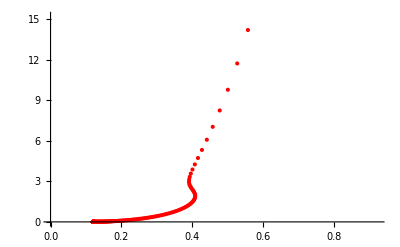

```mathematica
p3 = ListPlot[sofTϕM1Moved2try,PlotStyle->Red]
```

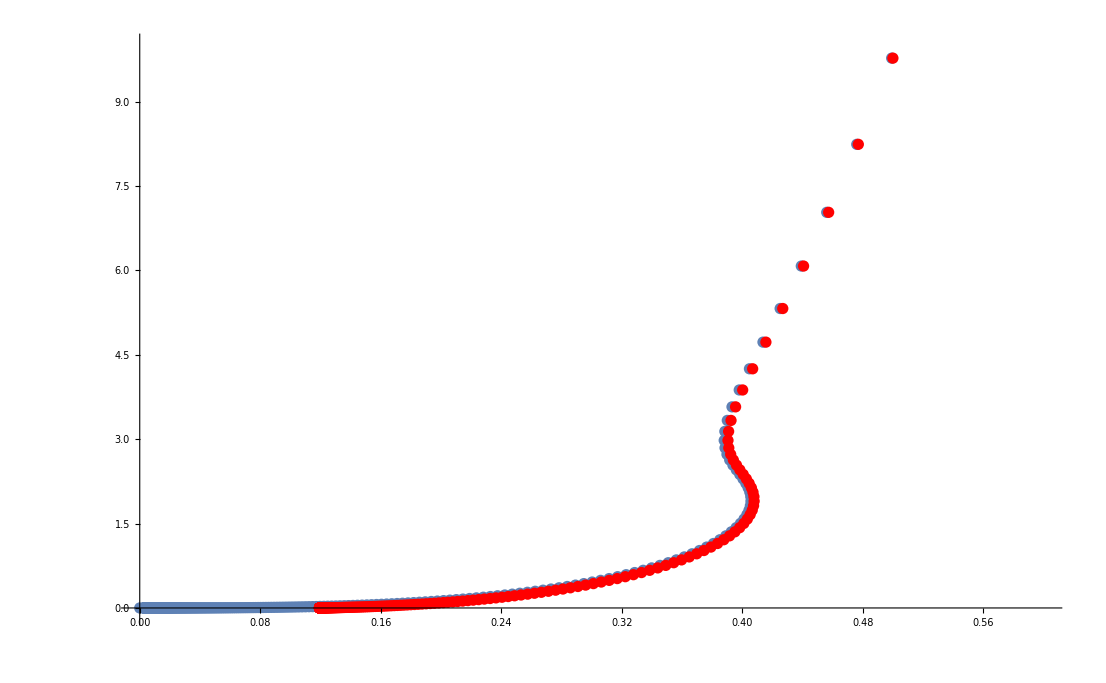

```mathematica
Show[p1,p3]
```

```mathematica
sofTϕM1Moved2try
```

{{70.8465,3.46379×10^7},{64.1213,2.56804×10^7},{58.0361,1.90409×10^7},{52.5299,1.41193×10^7},{47.5478,1.04708×10^7},{43.0397,7.76599×10^6},{38.9607,5.76057×10^6},{35.2698,4.27359×10^6},{31.9302,3.17091×10^6},{28.9084,2.35313×10^6},{26.1741,1.74657×10^6},{23.7001,1.29662×10^6},{21.4615,962801.},{19.436,715096.},{17.6032,531261.},{15.9448,394803.},{14.4443,293490.},{13.0866,218253.},{11.8581,162368.},{10.7465,120845.},{9.74075,89984.},{8.83072,67039.4},{8.00731,49974.3},{7.26229,37276.9},{6.5882,27825.1},{5.97829,20785.9},{5.42646,15540.5},{4.92718,11629.7},{4.47546,8711.82},{4.06678,6533.32},{3.69704,4905.56},{3.36254,3688.26},{3.05994,2777.07},{2.78621,2094.31},{2.53859,1582.15},{2.31463,1197.49},{2.11206,908.211},{1.92887,690.346},{1.76321,526.009},{1.61343,401.84},{1.47802,307.848},{1.35563,236.56},{1.24503,182.376},{1.14511,141.101},{1.05488,109.582},{0.973422,85.4525},{0.899935,66.9301},{0.833688,52.6721},{0.774032,41.6651},{0.720387,33.1427},{0.672238,26.5248},{0.629134,21.3708},{0.590677,17.3457},{0.55652,14.1942},{0.526356,11.7208},{0.499918,9.77558},{0.476963,8.24311},{0.457269,7.03407},{0.440623,6.07907},{0.426812,5.32394},{0.415622,4.72618},{0.40683,4.25228},{0.400202,3.87572},{0.395497,3.57537},{0.392469,3.33438},{0.39087,3.13926},{0.390455,2.97917},{0.390989,2.84542},{0.392245,2.73107},{0.394014,2.6306},{0.396102,2.53967},{0.398335,2.45495},{0.400559,2.37393},{0.402643,2.29481},{0.404476,2.21635},{0.405968,2.13779},{0.407051,2.05875},{0.407675,1.97913},{0.407808,1.89904},{0.407434,1.81874},{0.40655,1.73858},{0.405163,1.65895},{0.403291,1.58024},{0.400958,1.50285},{0.398194,1.42712},{0.395032,1.35335},{0.391507,1.2818},{0.387655,1.21268},{0.383513,1.14614},{0.379115,1.08228},{0.374497,1.02117},{0.36969,0.962834},{0.364725,0.907277},{0.359631,0.854467},{0.354434,0.804354},{0.349158,0.756872},{0.343825,0.711941},{0.338454,0.669474},{0.333065,0.629373},{0.327672,0.591541},{0.322291,0.555875},{0.316933,0.522273},{0.311611,0.490633},{0.306334,0.460853},{0.301111,0.432837},{0.29595,0.406489},{0.290856,0.381717},{0.285837,0.358433},{0.280896,0.336552},{0.276038,0.315993},{0.271266,0.29668},{0.266583,0.278538},{0.261992,0.261501},{0.257494,0.2455},{0.253091,0.230475},{0.248784,0.216367},{0.244574,0.203121},{0.24046,0.190685},{0.236444,0.179009},{0.232524,0.168047},{0.228702,0.157756},{0.224975,0.148096},{0.221345,0.139027},{0.217809,0.130513},{0.214366,0.122521},{0.211017,0.115019},{0.20776,0.107976},{0.204592,0.101365},{0.201515,0.0951583},{0.198524,0.0893323},{0.19562,0.0838632},{0.192801,0.0787291},{0.190066,0.0739096},{0.187412,0.0693853},{0.184839,0.0651381},{0.182344,0.0611511},{0.179926,0.0574083},{0.177583,0.0538946},{0.175315,0.0505962},{0.173118,0.0474998},{0.170992,0.0445929},{0.168935,0.041864},{0.166945,0.0393022},{0.165021,0.0368973},{0.163161,0.0346396},{0.161363,0.03252},{0.159627,0.0305303},{0.157949,0.0286623},{0.15633,0.0269086},{0.154766,0.0252623},{0.153257,0.0237167},{0.151802,0.0222657},{0.150398,0.0209036},{0.149045,0.0196247},{0.14774,0.0184242},{0.146484,0.0172971},{0.145273,0.0162389},{0.144107,0.0152455},{0.142984,0.0143129},{0.141904,0.0134373},{0.140864,0.0126154},{0.139865,0.0118437},{0.138903,0.0111192},{0.137979,0.010439},{0.137091,0.00980046},{0.136238,0.00920098},{0.135419,0.00863816},{0.134632,0.00810978},{0.133877,0.00761372},{0.133153,0.00714801},{0.132459,0.00671079},{0.131793,0.00630031},{0.131154,0.00591494},{0.130543,0.00555314},{0.129957,0.00521348},{0.129396,0.00489459},{0.128859,0.00459521},{0.128346,0.00431414},{0.127855,0.00405026},{0.127385,0.00380253},{0.126936,0.00356995},{0.126508,0.00335159},{0.126098,0.00314659},{0.125708,0.00295413},{0.125335,0.00277344},{0.12498,0.00260381},{0.124641,0.00244454},{0.124319,0.00229503},{0.124012,0.00215465},{0.123719,0.00202286},{0.123441,0.00189914},{0.123177,0.00178298},{0.122926,0.00167392},{0.122687,0.00157154},{0.122461,0.00147542},{0.122246,0.00138518},{0.122043,0.00130045},{0.12185,0.00122091},{0.121668,0.00114624},{0.121495,0.00107613},{0.121332,0.00101031},{0.121178,0.000948516},{0.121033,0.000890501},{0.120897,0.000836035},{0.120768,0.0007849},{0.120647,0.000736893},{0.120533,0.000691822},{0.120427,0.000649508},{0.120327,0.000609782},{0.120233,0.000572485},{0.120146,0.00053747},{0.120064,0.000504597},{0.119988,0.000473734},{0.119918,0.000444759},{0.119853,0.000417556},{0.119792,0.000392017},{0.119736,0.000368039},{0.119685,0.000345529},{0.119637,0.000324395},{0.119594,0.000304554},{0.119555,0.000285927},{0.119519,0.000268438},{0.119487,0.00025202},{0.119458,0.000236605},{0.119432,0.000222134},{0.119409,0.000208547},{0.119389,0.000195792},{0.119372,0.000183817},{0.119357,0.000172574},{0.119345,0.000162019},{0.119335,0.000152109},{0.119327,0.000142806},{0.119321,0.000134071},{0.119317,0.000125871},{0.119315,0.000118172},{0.119315,0.000110944},{0.119316,0.000104159},{0.119319,0.000097788},{0.119323,0.000091807},{0.119329,0.0000861918},{0.119335,0.00008092},{0.119344,0.0000759707},{0.119353,0.000071324},{0.119363,0.0000669616},{0.119374,0.000062866},{0.119386,0.0000590209},{0.119399,0.000055411},{0.119413,0.0000520219},{0.119427,0.0000488401},{0.119442,0.0000458529},{0.119458,0.0000430484},{0.119475,0.0000404154},{0.119491,0.0000379434},{0.119509,0.0000356227},{0.119527,0.0000334439},{0.119545,0.0000313984},{0.119563,0.0000294779},{0.119582,0.000027675},{0.119601,0.0000259823},{0.119621,0.0000243931},{0.119641,0.0000229012},{0.119661,0.0000215004},{0.119681,0.0000201854},{0.119701,0.0000189508},{0.119721,0.0000177917},{0.119742,0.0000167035},{0.119762,0.0000156819},{0.119783,0.0000147227},{0.119803,0.0000138222},{0.119824,0.0000129768},{0.119844,0.0000121831},{0.119865,0.0000114379},{0.119886,0.0000107384},{0.119906,0.0000100816},{0.119927,9.46495×10^-6},{0.119947,8.88605×10^-6},{0.119967,8.34255×10^-6},{0.119987,7.83229×10^-6},{0.120007,7.35324×10^-6},{0.120027,6.90349×10^-6},{0.120047,6.48125×10^-6},{0.120067,6.08484×10^-6},{0.120086,5.71267×10^-6},{0.120106,5.36326×10^-6},{0.120125,5.03523×10^-6},{0.120144,4.72726×10^-6},{0.120163,4.43812×10^-6},{0.120182,4.16667×10^-6},{0.1202,3.91183×10^-6},{0.120218,3.67257×10^-6},{0.120237,3.44794×10^-6},{0.120254,3.23705×10^-6},{0.120272,3.03906×10^-6},{0.12029,2.85319×10^-6},{0.120307,2.67868×10^-6},{0.120324,2.51484×10^-6},{0.120341,2.36102×10^-6},{0.120358,2.21662×10^-6},{0.120374,2.08104×10^-6},{0.120391,1.95376×10^-6},{0.120407,1.83426×10^-6},{0.120423,1.72207×10^-6},{0.120438,1.61674×10^-6},{0.120454,1.51786×10^-6},{0.120469,1.42502×10^-6},{0.120484,1.33786×10^-6},{0.120499,1.25603×10^-6},{0.120513,1.17921×10^-6},{0.120528,1.10708×10^-6},{0.120542,1.03937×10^-6},{0.120556,9.75805×10^-7},{0.120569,9.16121×10^-7},{0.120583,8.60081×10^-7},{0.120596,8.07482×10^-7},{0.120609,7.58094×10^-7},{0.120622,7.11727×10^-7},{0.120635,6.68192×10^-7},{0.120647,6.27321×10^-7},{0.12066,5.88953×10^-7},{0.120672,5.52931×10^-7},{0.120684,5.19106×10^-7},{0.120695,4.87363×10^-7},{0.120707,4.57555×10^-7},{0.120718,4.29578×10^-7},{0.120729,4.03296×10^-7},{0.12074,3.78635×10^-7},{0.120751,3.55471×10^-7},{0.120762,3.33729×10^-7},{0.120772,3.13316×10^-7},{0.120782,2.9416×10^-7},{0.120792,2.76162×10^-7},{0.121306,0}}

```mathematica
Export["C:\\Users\\pedro\\Desktop\\ESTUDIOS\\PhD in Theoretical Physics\\1 year\\S(T) Neural Network\\THE INVERTER\\NS_exp.txt",sofTϕM1Moved2try,"Table",FieldSeparators ->" "]
```

C:\Users\pedro\Desktop\ESTUDIOS\PhD in Theoretical Physics\1 year\S(T) Neural Network\THE INVERTER\NS_exp.txt

```mathematica
Export["C:\\Users\\pedro\\Desktop\\ESTUDIOS\\PhD in Theoretical Physics\\1 year\\S(T) Neural Network\\THE INVERTER\\NS_tanh.txt",sofTϕM1Moved,"Table",FieldSeparators ->" "]
```

C:\Users\pedro\Desktop\ESTUDIOS\PhD in Theoretical Physics\1 year\S(T) Neural Network\THE INVERTER\NS_tanh.txt

## Let us try a shift that will depend on S instead of depending on T

```mathematica
sofTϕM1 = Import["C:\\Users\\pedro\\Desktop\\ESTUDIOS\\PhD in Theoretical Physics\\1 year\\S(T) Neural Network\\Python Cacharreo run 2\\Curve_sofT_case3of5.csv"][[;; ;; 2]];
```

```mathematica
AppendTo[sofTϕM1,{0,0}];
```

```mathematica
p1 = ListPlot[sofTϕM1,PlotRange->{{0,0.6},{-0.1,10}}]
```

-Graphics-

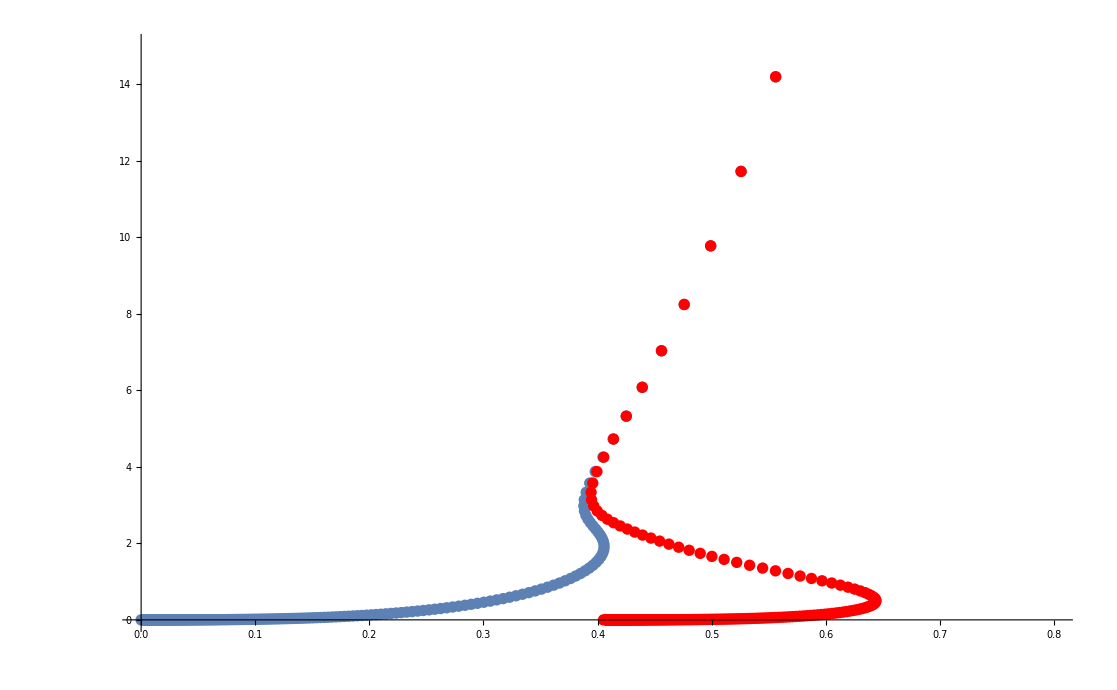

```mathematica
sofTϕM1Moved = {};
Do[AppendTo[sofTϕM1Moved,{sofTϕM1[[i,1]] + 0.46(1/2 +1/2 * Tanh[-1*(sofTϕM1[[i,2]]-1)]),sofTϕM1[[i,2]]}],{i,Length[sofTϕM1]}]
p2 =ListPlot[sofTϕM1Moved,PlotStyle->Red];
Show[p1,p2,PlotRange->{{0,0.8},{0,15}}]
```

```mathematica
sofTϕM1Moved
```

{{70.8465,3.46379×10^7},{64.1213,2.56804×10^7},{58.0361,1.90409×10^7},{52.5299,1.41193×10^7},{47.5478,1.04708×10^7},{43.0397,7.76599×10^6},{38.9607,5.76057×10^6},{35.2698,4.27359×10^6},{31.9302,3.17091×10^6},{28.9084,2.35313×10^6},{26.1741,1.74657×10^6},{23.7001,1.29662×10^6},{21.4615,962801.},{19.436,715096.},{17.6032,531261.},{15.9448,394803.},{14.4443,293490.},{13.0866,218253.},{11.8581,162368.},{10.7465,120845.},{9.74075,89984.},{8.83072,67039.4},{8.00731,49974.3},{7.26229,37276.9},{6.5882,27825.1},{5.97829,20785.9},{5.42646,15540.5},{4.92718,11629.7},{4.47546,8711.82},{4.06678,6533.32},{3.69704,4905.56},{3.36254,3688.26},{3.05994,2777.07},{2.78621,2094.31},{2.53859,1582.15},{2.31463,1197.49},{2.11206,908.211},{1.92887,690.346},{1.76321,526.009},{1.61343,401.84},{1.47802,307.848},{1.35563,236.56},{1.24503,182.376},{1.14511,141.101},{1.05487,109.582},{0.973415,85.4525},{0.89992,66.9301},{0.833659,52.6721},{0.773979,41.6651},{0.720296,33.1427},{0.672092,26.5248},{0.628909,21.3708},{0.590346,17.3457},{0.556053,14.1942},{0.525724,11.7208},{0.499093,9.77558},{0.475924,8.24311},{0.456003,7.03407},{0.439138,6.07907},{0.425164,5.32394},{0.413951,4.72618},{0.405398,4.25228},{0.399391,3.87572},{0.395767,3.57537},{0.39429,3.33438},{0.394664,3.13926},{0.396568,2.97917},{0.399694,2.84542},{0.403772,2.73107},{0.408584,2.6306},{0.413962,2.53967},{0.419789,2.45495},{0.425995,2.37393},{0.432543,2.29481},{0.439433,2.21635},{0.446686,2.13779},{0.454344,2.05875},{0.462455,1.97913},{0.471069,1.89904},{0.480219,1.81874},{0.489918,1.73858},{0.500144,1.65895},{0.510839,1.58024},{0.521906,1.50285},{0.53321,1.42712},{0.544592,1.35335},{0.555876,1.2818},{0.566884,1.21268},{0.577447,1.14614},{0.587418,1.08228},{0.596676,1.02117},{0.605131,0.962834},{0.612724,0.907277},{0.619426,0.854467},{0.625233,0.804354},{0.630162,0.756872},{0.634247,0.711941},{0.637531,0.669474},{0.640068,0.629373},{0.641915,0.591541},{0.643129,0.555875},{0.64377,0.522273},{0.643893,0.490633},{0.643552,0.460853},{0.642799,0.432837},{0.641679,0.406489},{0.640236,0.381717},{0.638509,0.358433},{0.636533,0.336552},{0.634343,0.315993},{0.631965,0.29668},{0.629427,0.278538},{0.626752,0.261501},{0.62396,0.2455},{0.621072,0.230475},{0.618102,0.216367},{0.615067,0.203121},{0.611979,0.190685},{0.60885,0.179009},{0.60569,0.168047},{0.60251,0.157756},{0.599316,0.148096},{0.596117,0.139027},{0.592918,0.130513},{0.589726,0.122521},{0.586546,0.115019},{0.583381,0.107976},{0.580236,0.101365},{0.577114,0.0951583},{0.574019,0.0893323},{0.570952,0.0838632},{0.567917,0.0787291},{0.564915,0.0739096},{0.561947,0.0693853},{0.559016,0.0651381},{0.556122,0.0611511},{0.553266,0.0574083},{0.55045,0.0538946},{0.547674,0.0505962},{0.544939,0.0474998},{0.542245,0.0445929},{0.539592,0.041864},{0.53698,0.0393022},{0.534411,0.0368973},{0.531883,0.0346396},{0.529396,0.03252},{0.526952,0.0305303},{0.524549,0.0286623},{0.522187,0.0269086},{0.519866,0.0252623},{0.517586,0.0237167},{0.515347,0.0222657},{0.513147,0.0209036},{0.510987,0.0196247},{0.508866,0.0184242},{0.506784,0.0172971},{0.504741,0.0162389},{0.502735,0.0152455},{0.500767,0.0143129},{0.498836,0.0134373},{0.496941,0.0126154},{0.495083,0.0118437},{0.493259,0.0111192},{0.491471,0.010439},{0.489716,0.00980046},{0.487996,0.00920098},{0.486309,0.00863816},{0.484655,0.00810978},{0.483033,0.00761372},{0.481442,0.00714801},{0.479883,0.00671079},{0.478355,0.00630031},{0.476856,0.00591494},{0.475388,0.00555314},{0.473948,0.00521348},{0.472537,0.00489459},{0.471154,0.00459521},{0.469799,0.00431414},{0.46847,0.00405026},{0.467168,0.00380253},{0.465893,0.00356995},{0.464643,0.00335159},{0.463418,0.00314659},{0.462218,0.00295413},{0.461042,0.00277344},{0.459889,0.00260381},{0.458761,0.00244454},{0.457654,0.00229503},{0.456571,0.00215465},{0.455509,0.00202286},{0.454469,0.00189914},{0.45345,0.00178298},{0.452452,0.00167392},{0.451474,0.00157154},{0.450516,0.00147542},{0.449578,0.00138518},{0.448659,0.00130045},{0.447759,0.00122091},{0.446877,0.00114624},{0.446013,0.00107613},{0.445167,0.00101031},{0.444338,0.000948516},{0.443526,0.000890501},{0.442731,0.000836035},{0.441952,0.0007849},{0.44119,0.000736893},{0.440443,0.000691822},{0.439711,0.000649508},{0.438994,0.000609782},{0.438293,0.000572485},{0.437605,0.00053747},{0.436932,0.000504597},{0.436273,0.000473734},{0.435627,0.000444759},{0.434995,0.000417556},{0.434375,0.000392017},{0.433769,0.000368039},{0.433175,0.000345529},{0.432593,0.000324395},{0.432023,0.000304554},{0.431465,0.000285927},{0.430919,0.000268438},{0.430384,0.00025202},{0.42986,0.000236605},{0.429347,0.000222134},{0.428844,0.000208547},{0.428352,0.000195792},{0.42787,0.000183817},{0.427398,0.000172574},{0.426936,0.000162019},{0.426484,0.000152109},{0.42604,0.000142806},{0.425606,0.000134071},{0.425181,0.000125871},{0.424765,0.000118172},{0.424358,0.000110944},{0.423959,0.000104159},{0.423568,0.000097788},{0.423185,0.000091807},{0.42281,0.0000861918},{0.422443,0.00008092},{0.422084,0.0000759707},{0.421732,0.000071324},{0.421388,0.0000669616},{0.42105,0.000062866},{0.42072,0.0000590209},{0.420396,0.000055411},{0.420079,0.0000520219},{0.419769,0.0000488401},{0.419465,0.0000458529},{0.419168,0.0000430484},{0.418876,0.0000404154},{0.418591,0.0000379434},{0.418312,0.0000356227},{0.418038,0.0000334439},{0.417771,0.0000313984},{0.417508,0.0000294779},{0.417251,0.000027675},{0.417,0.0000259823},{0.416754,0.0000243931},{0.416513,0.0000229012},{0.416276,0.0000215004},{0.416045,0.0000201854},{0.415819,0.0000189508},{0.415597,0.0000177917},{0.41538,0.0000167035},{0.415168,0.0000156819},{0.414959,0.0000147227},{0.414756,0.0000138222},{0.414556,0.0000129768},{0.414361,0.0000121831},{0.414169,0.0000114379},{0.413982,0.0000107384},{0.413798,0.0000100816},{0.413619,9.46495×10^-6},{0.413443,8.88605×10^-6},{0.413271,8.34255×10^-6},{0.413102,7.83229×10^-6},{0.412937,7.35324×10^-6},{0.412775,6.90349×10^-6},{0.412617,6.48125×10^-6},{0.412462,6.08484×10^-6},{0.41231,5.71267×10^-6},{0.412161,5.36326×10^-6},{0.412015,5.03523×10^-6},{0.411873,4.72726×10^-6},{0.411733,4.43812×10^-6},{0.411597,4.16667×10^-6},{0.411463,3.91183×10^-6},{0.411332,3.67257×10^-6},{0.411203,3.44794×10^-6},{0.411078,3.23705×10^-6},{0.410955,3.03906×10^-6},{0.410834,2.85319×10^-6},{0.410716,2.67868×10^-6},{0.410601,2.51484×10^-6},{0.410488,2.36102×10^-6},{0.410377,2.21662×10^-6},{0.410268,2.08104×10^-6},{0.410162,1.95376×10^-6},{0.410058,1.83426×10^-6},{0.409956,1.72207×10^-6},{0.409857,1.61674×10^-6},{0.409759,1.51786×10^-6},{0.409663,1.42502×10^-6},{0.40957,1.33786×10^-6},{0.409478,1.25603×10^-6},{0.409388,1.17921×10^-6},{0.409301,1.10708×10^-6},{0.409214,1.03937×10^-6},{0.40913,9.75805×10^-7},{0.409048,9.16121×10^-7},{0.408967,8.60081×10^-7},{0.408888,8.07482×10^-7},{0.40881,7.58094×10^-7},{0.408734,7.11727×10^-7},{0.40866,6.68192×10^-7},{0.408587,6.27321×10^-7},{0.408516,5.88953×10^-7},{0.408447,5.52931×10^-7},{0.408378,5.19106×10^-7},{0.408311,4.87363×10^-7},{0.408246,4.57555×10^-7},{0.408182,4.29578×10^-7},{0.408119,4.03296×10^-7},{0.408058,3.78635×10^-7},{0.407997,3.55471×10^-7},{0.407938,3.33729×10^-7},{0.407881,3.13316×10^-7},{0.407824,2.9416×10^-7},{0.407769,2.76162×10^-7},{0.405167,0}}

General::munfl: Exp[-3.46379×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.56804×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.90409×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

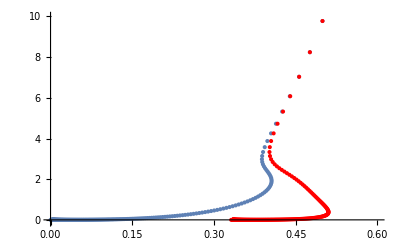

```mathematica
sofTϕM1Moved2try = {};
Do[AppendTo[sofTϕM1Moved2try,{sofTϕM1[[i,1]] + 0.3* Exp[-(sofTϕM1[[i,2]]-0.1)/1],sofTϕM1[[i,2]]}],{i,Length[sofTϕM1]}]
p3 = ListPlot[sofTϕM1Moved2try,PlotStyle->Red];
Show[p1,p3]
```

Let us import the potential

```mathematica
ReconstructedPotential1=Import["C:\\Users\\pedro\\Desktop\\ESTUDIOS\\PhD in Theoretical Physics\\1 year\\S(T) Neural Network\\nyx stuff\\NS\\NS_exp\\V_epoch 1000000.csv"][[2;;]];
```

```mathematica
RRR={};
Do[AppendTo[RRR,{2ReconstructedPotential1[[i,1]],4ReconstructedPotential1[[i,2]]}],{i,1,Dimensions[ReconstructedPotential1][[1]]}];
V=Interpolation[RRR];
```

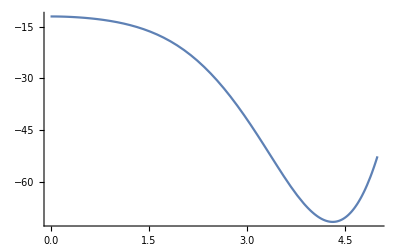

```mathematica
Plot[V[x],{x,0,5}]
```

## Try it with ϕM = 2.0

```mathematica
sofTϕM2 = Import["C:\\Users\\pedro\\Desktop\\ESTUDIOS\\PhD in Theoretical Physics\\1 year\\S(T) Neural Network\\THE INVERTER\\Thermo curves\\SofTphiM2_0.txt","Table"][[;; ;; 2]];
```

```mathematica
AppendTo[sofTϕM2,{0,0}];
```

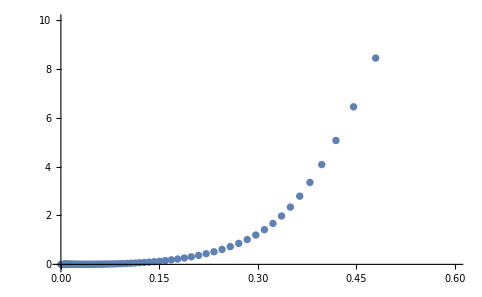

```mathematica
p1 = ListPlot[sofTϕM2,PlotRange->{{0,0.6},{-0.1,10}}]
```

General::munfl: 0.1 3.516080924403234278083025969×10^-311 is too small to represent as a normalized machine number; precision may be lost.

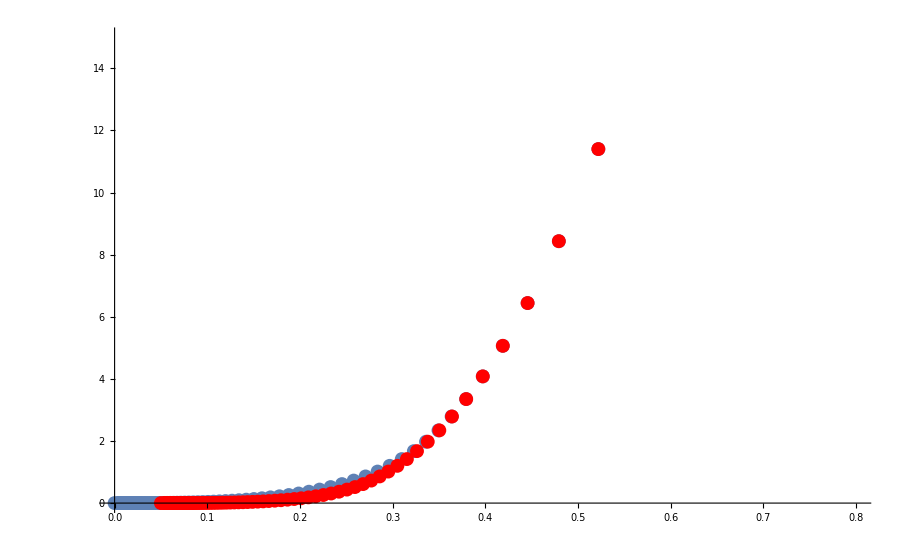

```mathematica
sofTϕM2Moved = {};
Do[AppendTo[sofTϕM2Moved,{sofTϕM2[[i,1]] + 0.1(1/2 +1/2 * Tanh[-1*(sofTϕM2[[i,2]])]),sofTϕM2[[i,2]]}],{i,Length[sofTϕM2]}]
p2 =ListPlot[sofTϕM2Moved,PlotStyle->Red];
Show[p1,p2,PlotRange->{{0,0.8},{0,15}}]
```

```mathematica
Export["C:\\Users\\pedro\\Desktop\\ESTUDIOS\\PhD in Theoretical Physics\\1 year\\S(T) Neural Network\\THE INVERTER\\NS_easy.txt",sofTϕM2Moved,"Table",FieldSeparators ->" "]
```

C:\Users\pedro\Desktop\ESTUDIOS\PhD in Theoretical Physics\1 year\S(T) Neural Network\THE INVERTER\NS_easy.txt

Let us do with ϕ_M = 2 again but using another function, like an exponential

```mathematica
sofTϕM2 = Import["C:\\Users\\pedro\\Desktop\\ESTUDIOS\\PhD in Theoretical Physics\\1 year\\S(T) Neural Network\\THE INVERTER\\Thermo curves\\SofTphiM2_0.txt","Table"][[;; ;; 2]];
```

```mathematica
AppendTo[sofTϕM2,{0,0}];
```

```mathematica
p1 = ListPlot[sofTϕM2,PlotRange->{{0,0.6},{-0.1,10}}]
```

-Graphics-

General::munfl: 0.1 3.516080924403234278083025969×10^-311 is too small to represent as a normalized machine number; precision may be lost.

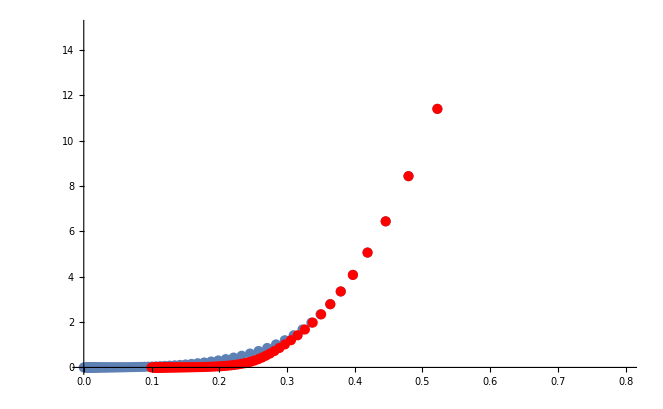

```mathematica
sofTϕM2Moved = {};
Do[AppendTo[sofTϕM2Moved,{sofTϕM2[[i,1]]  + 0.1*Exp[-2*sofTϕM2[[i,2]]],sofTϕM2[[i,2]]}],{i,Length[sofTϕM2]}]
p2 =ListPlot[sofTϕM2Moved,PlotStyle->Red];
Show[p1,p2,PlotRange->{{0,0.8},{0,15}}]
```

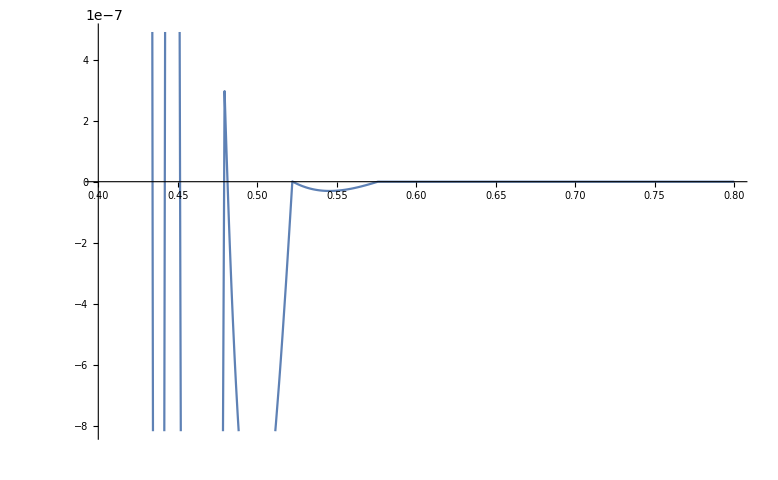

```mathematica
i1 = Interpolation[sofTϕM2];i2 = Interpolation[sofTϕM2Moved];
Plot[i1[x]-i2[x],{x,0.4,0.8}]
```

```mathematica
ListLogPlot[sofTϕM2Moved-sofTϕM2]
```

-Graphics-

```mathematica
sofTϕM2Moved-sofTϕM2
```

{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{1.11022×10^-16,0.},{1.04114×10^-11,0.},{1.2093×10^-8,0.},{1.11853×10^-6,0.},{0.0000217261,0.},{0.000159318,0.},{0.000631633,0.},{0.00169066,0.},{0.00350818,0.},{0.00615101,0.},{0.00961393,0.},{0.0138473,0.},{0.0187645,0.},{0.0242418,0.},{0.0301231,0.},{0.0362328,0.},{0.0423933,0.},{0.0484422,0.},{0.0542445,0.},{0.0596985,0.},{0.0647369,0.},{0.069323,0.},{0.0734455,0.},{0.0771122,0.},{0.0803448,0.},{0.0831735,0.},{0.0856334,0.},{0.0877613,0.},{0.089594,0.},{0.0911665,0.},{0.0925117,0.},{0.0936594,0.},{0.0946364,0.},{0.0954667,0.},{0.0961711,0.},{0.0967679,0.},{0.0972731,0.},{0.0977003,0.},{0.0980612,0.},{0.098366,0.},{0.0986232,0.},{0.0988402,0.},{0.0990231,0.},{0.0991773,0.},{0.0993073,0.},{0.0994168,0.},{0.099509,0.},{0.0995867,0.},{0.0996521,0.},{0.0997072,0.},{0.0997535,0.},{0.0997926,0.},{0.0998254,0.},{0.0998531,0.},{0.0998764,0.},{0.0998959,0.},{0.0999124,0.},{0.0999263,0.},{0.099938,0.},{0.0999478,0.},{0.0999561,0.},{0.099963,0.},{0.0999689,0.},{0.0999738,0.},{0.099978,0.},{0.0999815,0.},{0.0999844,0.},{0.0999869,0.},{0.099989,0.},{0.0999907,0.},{0.0999922,0.},{0.0999934,0.},{0.0999945,0.},{0.0999953,0.},{0.0999961,0.},{0.0999967,0.},{0.0999972,0.},{0.0999977,0.},{0.099998,0.},{0.0999983,0.},{0.0999986,0.},{0.0999988,0.},{0.099999,0.},{0.0999992,0.},{0.0999993,0.},{0.0999994,0.},{0.0999995,0.},{0.0999996,0.},{0.0999997,0.},{0.0999997,0.},{0.1,0}}

```mathematica
Export["C:\\Users\\pedro\\Desktop\\ESTUDIOS\\PhD in Theoretical Physics\\1 year\\S(T) Neural Network\\THE INVERTER\\NS_easy_exp.txt",sofTϕM2Moved,"Table",FieldSeparators ->" "]
```

C:\Users\pedro\Desktop\ESTUDIOS\PhD in Theoretical Physics\1 year\S(T) Neural Network\THE INVERTER\NS_easy_exp.txt